# 1st SE for BEC Polaron

## Parameters and Equations

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx;
```

## 1st Order

## Q Integral

```mathematica
Integrand[q1_,τ_] := 1/(2*Pi)^3*vq2[q1]*dq[q1,0,τ]*g0[q1,0,τ];
```

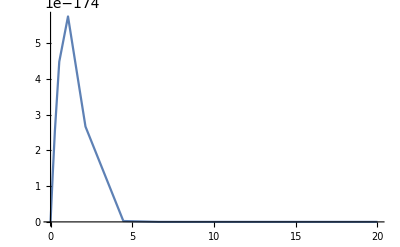

```mathematica
Plot[Integrand[q1,0.5],{q1,0,20}, PlotPoints->10, MaxRecursion->4, PlotRange->Full]
```

```mathematica
se[τ_]:=NIntegrate[4*Pi*q1^2*Integrand[q1,τ],{q1,0,qc} ];
```

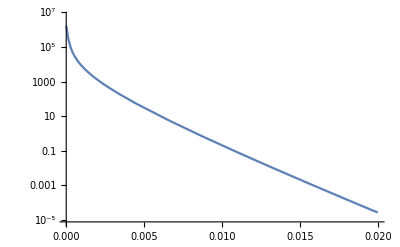

```mathematica
LogPlot[se[τ],{τ,0,0.02}, PlotPoints->10, MaxRecursion->4, PlotRange->Full, PlotLegends->"SeExp"]
```

## Data Output

```mathematica
sedata = Table[{τ, se[τ]},{τ, 0, 0.02, 0.0001}];
```

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/BEC"];
DumpSave["BEC_1st_seonly.mx", {sedata}];
Export["mat_BEC_1st_seonly", se, "Table"];
```